## myPackage

```mathematica
(*generated 2025-06-13, by Dr.Carl Firle, MD*)
filename="data_preparation";
CloudGet[CloudObject["https://www.wolframcloud.com/obj/firlecarl/myPackageWL.wl"]]

myFontSize=13
myFontStandard="Lucida Sans Unicode"

myStyle["Wolfram Mathematica Version 14.2",22,Background->Yellow]
(*myColorFavorits=TableForm[Table[ColorData[i],{i,{3,24,35,61,97,106,114}}]] Table[ContourPlot[x+Sin[x^2+y^2],{x,-4,4},{y,-4,4},Contours->9,ContourShading->ColorData[i,"ColorList"]],{i,{3,24,35,61,97,106,114}}] myColorGradientFavorits=Table[DensityPlot[y+Sin[x^2+3y],{x,-3,3},{y,-3,3},ColorFunction->ColorData[i]],{i,{"RedBlueTones","Rainbow","DarkRainbow","DarkBands","BrightBands","CMYKColors","Pastel","GrayTones"}}] Table[ColorData[i,"Image"],{i,{"DarkRainbow","Pastel"}}]*)

myColors=ColorData[61]
myColorForGradient=ColorData["DarkRainbow"]
myCMYKColors[]
myBAUAColors[4]
myPureColors[]

myExportFigureList={};
myExportEquationList={};

impPath=Directory[]~~"\\Desktop\\source\\" (*path of source*)
exPath=Directory[]~~"\\Desktop\\output\\" (*path of output*)

pathSaveVersions=Directory[]~~"\\Desktop\\backup\\" (*path of backup*)
NotebookOpen[CloudObject["https://www.wolframcloud.com/obj/firlecarl/myBackup.nb"]]

NotebookSave[EvaluationNotebook[],Directory[]~~"\\Desktop\\"~~filename~~".nb"]

myPackageInputPrint[]
```

13

Lucida Sans Unicode

Wolfram Mathematica Version 14.2

ColorDataFunction[…]

ColorDataFunction[…]

{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]}

{RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.9568627450980393, 0.9529411764705882, 0.9254901960784314],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764],RGBColor[0.00392156862745098, 0.3607843137254902, 0.5764705882352941],RGBColor[0.6509803921568628, 0.8196078431372549, 0.9450980392156862],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431]}

{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0],RGBColor[0, 1, 1],RGBColor[1, 0, 1],RGBColor[1, 1, 0],GrayLevel[0]}

C:\Users\mona_\Desktop\source\

C:\Users\mona_\Desktop\output\

C:\Users\mona_\Desktop\backup\

## myFigureIDs

```mathematica
IntegerString[#,10,3]&/@Range[50]  (*make the next output cell to an input cell with the variable myFigureIDs myFigureIDs=*)
```

```mathematica
myFigureIDs={"001","002","003","004","005","006","007","008","009","010","011","012","013","014","015","016","017","018","019","020","021","022","023","024","025","026","027","028","029","030","031","032","033","034","035","036","037","038","039","040","041","042","043","044","045","046","047","048","049","050"};
```

## data import

```mathematica
synchronize=.
synchronize[l_List,timePosition_Integer,maxTime_,timeStamp_]:=Module[{l2}
,l2=l
;l2[[All,timePosition]]=Map[Round[timeStamp-Quantity[(maxTime-#),"Seconds"],.5]&,l2[[All,timePosition]]];
l2]

protocolSelect=.
protocolSelect[varName_String]:=Select[protocol,StringContainsQ[Keys[#],varName]&]

oneTableAppend=.
oneTableAppend[varNamesList_List,lValues_List]:=Module[{replList,temp,temp2}
,varNames=Flatten[Append[varNames,varNamesList]]
;temp=FirstPosition[oneTable[[All,1]],#[[1]]][[1]]&/@lValues
;replList=oneTable[[#[[1]]]]->Append[oneTable[[#[[1]]]],#[[2,2;;-1]]]&/@Transpose[{temp,lValues}]
;temp2=myFlatten[oneTable/.replList,1]
;oneTable=PadRight[temp2,{Length[oneTable[[All,1]]],Length[oneTable[[1]]]+Length[varNamesList]},{Missing[]}]
]
(*first column is KeyColumn (elapsed time), values are added and constant array is created by adding Missing[]*)

urlHead="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2024_effects-mask-wearing/20250606-01_air-cleaner-test/";
```

```mathematica
dProtocol=Import[urlHead ~~"%23testdata_protocol.txt"];
```

```mathematica
protocol=#[[1]]->Quantity[ToExpression[#[[2]]],"Seconds"]&/@myStringSplit[dProtocol,{" --- "," :: "}];
protocol=#[[1]]->#[[2]]-Min[Values@protocol]&/@protocol
```

{start time***Fri Jun 13 2025 14:58:41 GMT+0200 (Mitteleuropäische Sommerzeit)→0 s,airCleaner_Airlock_start→1236671 s,airCleaner_cabin_start→1237464 s,roomAirCondition_start→1237656 s,AS_01_start→1238008 s,AS_02_start→1238320 s,AS_03_start→1238510 s,AS_01_start→1241399 s,mask_order***surgical mask,30, ,FFP2 mask,50, ,none,30, ,FFP2 mask,30, ,surgical mask,50, ,none,50, →1249924 s,randomise_start→1249924 s,mask_type***surgical mask***-→1250390 s,target_respMinVol***30***l/min→1250599 s,measurement_start***surgical mask***30→1250774 s,door_airlock_open→1250937 s,door_airlock_closed→1251096 s,door_cabin_open→1251301 s,subject_in_position→1251476 s,door_cabin_closed→1251865 s,door_airlock_open→1252074 s,door_airlock_closed→1252278 s,airCleaner_cabin_end→1252455 s,load_total***50→1252763 s,load_start***50***Watt→1252763 s,load_total***75→1253036 s,load_increase***25***Watt→1253036 s,load_total***100→1253223 s,load_increase***25***Watt→1253223 s,countdown_start***.1***min→1260952 s,pexa_start→1264895 s,pexa_sample_start→1265341 s,pexa_sample_end→1265660 s,load_total***75→1266229 s,load_decrease***25***Watt→1266229 s,load_total***50→1266409 s,load_decrease***25***Watt→1266410 s,load_total***25→1266812 s,load_decrease***25***Watt→1266812 s,exercise_end→1266989 s,pexa_end→1267882 s,measurement_end→1268253 s,door_cabin_exit_open→1268469 s,subject_exits→1268668 s,airCleaner_airlock_end→1269055 s,door_airlock_open→1269404 s,door_cabin_open→1269694 s,window_opening→1269893 s,window_closing→1270091 s,door_cabin_closed→1270270 s,door_airlock_closed→1270440 s,door_cabin_exit_closed→1270627 s,airCleaner_Airlock_start→1270833 s,airCleaner_cabin_start→1271087 s,next_measurement→1271400 s,door_cabin_exit_open→1275976 s,subject_exits→1276123 s,airCleaner_Airlock_end→1276304 s,roomAirCondition_end→1276479 s,AS_01_end→1276642 s,AS_02_end→1277002 s,AS_03_end→1277359 s,AS_01_name***11f→1288599 s,AS_02_name***→1288599 s,AS_03_name***→1288599 s,yearOfBirth***1955→1288599 s,gender***female→1288599 s,height***→1288600 s,weight***→1288600 s,healthy***1→1288600 s,fever***0→1288600 s,illness***0→1288600 s,surgeries***0→1288600 s,cardiovascular***0→1288600 s,infarction***0→1288600 s,aneurysma***0→1288600 s,pneumothorax***0→1288600 s,dizziness***0→1288600 s,respDisease***0→1288600 s,acuteRespDisease***0→1288600 s,allergies***0→1288600 s,nicotineAbuse***0→1288600 s,medication***0→1288600 s,auscultationHeart***distinct &amp; clear sounds, regular rhythm, normal heart rate, no abnormal sounds→1288600 s,heartRate***→1288600 s,rhythm***SA node→1288600 s,cardiacAxis***normal→1288600 s,heartBlock***none→1288600 s,rWave***regular R-wave progression→1288600 s,repolarisation***none→1288601 s,auscultationLung***vesicular sound, normopnoea, no pathological breath sound→1288601 s,end of protocol→1288601 s}

```mathematica
timeline=Range[0,(Values[protocolSelect["end of protocol"]]-Values[protocolSelect["start time"]]) [[1]][[1]],.5]//Short
varNames={"elapsed time"};
(*the time points in protocol were altered manually to ensure whole time line for test data*)
oneTable=List/@timeline
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,«2577185»,1.2886×10^6,1.2886×10^6,1.2886×10^6,1.2886×10^6,1.2886×10^6,1.2886×10^6,1.2886×10^6,1.2886×10^6,1.2886×10^6}

{{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,«2577185»,1.2886×10^6,1.2886×10^6,1.2886×10^6,1.2886×10^6,1.2886×10^6,1.2886×10^6,1.2886×10^6,1.2886×10^6,1.2886×10^6}}

```mathematica
timeline=Quantity[#,"Seconds"]&/@Range[0,1500,.5];
varNames={"elapsed time"};
oneTable=List/@timeline;
```

```mathematica
dSensirion=Import[urlHead ~~"2025-06-19_15-42-56-CC_AllSensors.edf","Text"];
dSensirion=myStringSplit[dSensirion,{"\n","\t"}];
dSensirion[[11;;-1]]=Flatten[{ToExpression[#[[1]]],FromDateString[#[[2]]],ToExpression[#[[3;;-1]]]}]&/@dSensirion[[11;;-1]];
dSensirionVarNames=Delete[dSensirion[[10]],2];
```

```mathematica
dSensirionSync=synchronize[dSensirion[[11;;-1]],1,Max[dSensirion[[11;;-1]][[All,1]]],UnitConvert["AS_02_end"/. protocol,"Seconds"]];
```

```mathematica
(*the timeline in test protocol is too wide*)
dSensirionSync=synchronize[dSensirion[[11;;-1]],1,Max[dSensirion[[11;;-1]][[All,1]]],Quantity[200,"Seconds"]];
```

```mathematica
dSensirionSync=myFlatten[Transpose[{Delete[Union/@(Transpose/@GatherBy[dSensirionSync,First][[All,All,1]]),-1],Delete[(Transpose/@GatherBy[dSensirionSync,First][[All,All,3;;-1]]) /. Null->Nothing,-1]}],1];

sensirionPositionList=Map[Position[dSensirionVarNames,#][[1,1]]&,sensirionVarNamesMassNum=SplitBy[(Select[dSensirionVarNames,StringContainsQ[#,Union[Last[StringSplit[#,"_"]]&/@Rest@dSensirionVarNames]]&&StringContainsQ[#,"TypPartSize"]==False&]),StringContainsQ[#,"Mass"]&],{2}]
```

{{2,3,4,5},{6,7,8,9,10},{12,13,14,15},{16,17,18,19,20},{22,23,24,25},{26,27,28,29,30},{32,33,34,35},{36,37,38,39,40},{42,43,44,45},{46,47,48,49,50},{52,53,54,55},{56,57,58,59,60},{62,63,64,65},{66,67,68,69,70},{72,73,74,75},{76,77,78,79,80}}

```mathematica
(*data sheet https://sensirion.com/media/documents/8600FF88/64A3B8D6/Sensirion_PM_Sensors_Datasheet_SPS30.pdf and statementhttps://sensirion.com/media/documents/8600FF88/64A3B8D6/Sensirion_PM_Sensors_Datasheet_SPS30.pdfNonehttps://sensirion.com/media/documents/8600FF88/64A3B8D6/Sensirion_PM_Sensors_Datasheet_SPS30.pdfHyperlinkActionRecycledHyperlinkActive and precision
 https://sensirion.com/resource/application_note/pm/sensor_specificationhttps://sensirion.com/resource/application_note/pm/sensor_specificationNonehttps://sensirion.com/resource/application_note/pm/sensor_specificationHyperlinkActionRecycledHyperlinkActive*)

errorMassConcSensirionLowPM=.
errorMassConcSensirionLowPM[n_Real]:=Which[0<n<=100,Around[n,n .05 + 5],100<n<=1000,Around[n,n 0.10],True,n]

errorMassConcSensirionHighPM=.
errorMassConcSensirionHighPM[n_Real]:=Which[0<n<=100,Around[n,25],100<n<=1000,Around[n,n 0.25],True,n]

errorNumConcSensirionLowPM=.
errorNumConcSensirionLowPM[n_Real]:=Which[n<=1000,Around[n,100],1000<n<=3000,Around[n,n 0.10],True,n]

errorNumConcSensirionHighPM=.
errorNumConcSensirionHighPM[n_Real]:=Which[n<=1000,Around[n,250],1000<n<=3000,Around[n,n 0.25],True,n]

errorSensirion=.
errorSensirion[l_List/;Length[l]==4]:={errorMassConcSensirionLowPM[#[[1]]],errorMassConcSensirionLowPM[#[[2]]]-errorMassConcSensirionLowPM[#[[1]]],errorMassConcSensirionHighPM[#[[3]]]-errorMassConcSensirionLowPM[#[[2]]],errorMassConcSensirionHighPM[#[[4]]]-errorMassConcSensirionHighPM[#[[3]]]}&@l

errorSensirion[l_List/;Length[l]==5]:=
{errorNumConcSensirionLowPM[#[[1]]],errorNumConcSensirionLowPM[#[[2]]]-errorNumConcSensirionLowPM[#[[1]]],errorNumConcSensirionLowPM[#[[3]]]-errorNumConcSensirionLowPM[#[[2]]],errorNumConcSensirionHighPM[#[[4]]]-errorNumConcSensirionLowPM[#[[3]]],errorNumConcSensirionHighPM[#[[5]]]-errorNumConcSensirionHighPM[#[[4]]]}&@l

dErrorSensirion=Map[errorSensirion[#]&,dSensirionSync[[All,First[#];;Last[#]]]&/@sensirionPositionList,{2}];

dErrorSensirion=Prepend[myFlatten[Transpose[{dSensirionSync[[All,1]],Transpose[dErrorSensirion]}],1],Prepend[Flatten[sensirionVarNamesMassNum],dSensirionVarNames[[1]]]];
```

```mathematica
oneTableAppend[Rest[First[dErrorSensirion]],Rest@dErrorSensirion]
```

```mathematica
dGrimm=Import[urlHead ~~"11-D_2025-06-06-C.dat","Text"];
dGrimm=myStringSplit[StringReplace[dGrimm,","->"."],{"\n","\t"}];

dGrimm[[16;;-1]]=Flatten[{UnixTime[FromDateString[#[[1]]]],ToExpression[#[[2;;-1]]]}]&/@dGrimm[[16;;-1]];
(*Device specification Grimm 11-Dhttps://grimm-aerosol.ca/data/documents/Grimm-11-D-Datasheet.pdfNonehttps://grimm-aerosol.ca/data/documents/Grimm-11-D-Datasheet.pdfHyperlinkActionRecycledHyperlinkActive*)
```

```mathematica
dGrimmSync=synchronize[dGrimm[[16;;-1]],1,Max[dGrimm[[16;;-1]][[All,1]]],UnitConvert["AS_01_end"/. protocol,"Seconds"]];
```

```mathematica
(*the timeline in test protocol is too wide*)
dGrimmSync=synchronize[dGrimm[[16;;-1]],1,Max[dGrimm[[16;;-1]][[All,1]]],Quantity[1300,"Seconds"]];
```

```mathematica
dErrorGrimm=myFlatten[Transpose[{dGrimmSync[[All,1]],Map[Around[#,#.1]&,(dGrimmSync[[All,2;;-1]]),{2}]}] ,1];(*error of 10 %*)
```

```mathematica
dGrimm[[5;;20]]
```

{{Model: 11-D},{Serial No.: 11D20167},{Firmware revision: 12.50E},{Software revision: 1179-V2.05 (15-06-2020)},{Unit: counts/liter (differential)},{C-factor: 1.00},{location factor: 1.00},{Comment: F2583},{online data},{<Data>},{[d&t31.12.2035 11:50:55],0.253 um,0.298 um,0.352 um,0.414 um,0.488 um,0.576 um,0.679 um,0.800 um,0.943 um,1.112 um,1.310 um,1.545 um,1.821 um,2.146 um,2.530 um,2.982 um,3.515 um,4.144 um,4.884 um,5.757 um,6.787 um,8.000 um,9.430 um,11.12 um,13.10 um,15.45 um,18.21 um,21.46 um,25.30 um,29.82 um,35.15 um},{1749216301,10270.,3410.,2250.,1300.,550.,100.,200.,0.,0.,0.,50.,50.,0.,0.,0.,0.,0.,0.,10.,10.,20.,0.,10.,0.,0.,0.,0.,0.,0.,0.,0.},{1749216307,10520.,3610.,2250.,1000.,250.,200.,0.,100.,150.,50.,0.,0.,0.,50.,0.,10.,20.,20.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1749216313,10470.,3810.,2300.,950.,450.,200.,200.,0.,50.,0.,50.,0.,50.,100.,0.,0.,0.,0.,0.,0.,0.,0.,20.,10.,20.,0.,0.,0.,0.,0.,0.},{1749216319,9420.,3360.,1900.,1100.,400.,350.,50.,0.,100.,100.,0.,100.,100.,50.,70.,100.,10.,0.,0.,20.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1749216325,10320.,3010.,2100.,1250.,650.,250.,200.,100.,50.,0.,100.,150.,0.,50.,0.,0.,0.,0.,0.,10.,20.,10.,0.,10.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
UnitConvert[Quantity[1.27537*^6, "Seconds"],"hours"]
```

354.269 h

```mathematica
{dErrorGrimm[[All,1]],Total/@dErrorGrimm[[All,2;;-1]]}ᵀ
```

```mathematica
MinMax[dErrorGrimm[[All,1]]]
```

{1.27537×10^6 s,1.27664×10^6 s}

```mathematica
ListFitPlot[{dErrorGrimm[[All,1]],Total/@dErrorGrimm[[All,2;;-1]]}ᵀ,myPlotSequence[],FrameLabel->{"time [s]", "total particle count [1 cm^-3]"},PlotFitElements->"BandCurves"]
```

-Graphics-

the  timeline is flawed because protocol data is probationary . I refrain from concrete analysis...

```mathematica
oneTableAppend[dGrimm[[15]],dErrorGrimm]
```

```mathematica
Length@varNames
```

112

```mathematica
Union[Length/@oneTable]
```

{112}

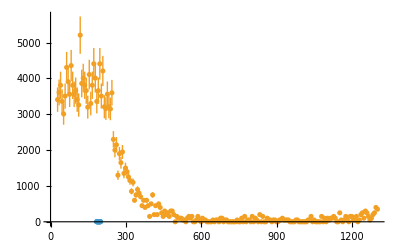

```mathematica
ListPlot[{Transpose@{oneTable[[All,1]],oneTable[[All,2]]},Transpose@{oneTable[[All,1]],oneTable[[All,-31]]}}]
```

```mathematica
dtesto=Import[urlHead ~~"testo435%202025-06-20%2014-35.csv","Text"];
dtesto=myStringSplit[StringReplace[dtesto,","->"."],{"\n",";"}];
dtestoVarNames=dtesto[[1]][[4;;-1]];
dtesto=Flatten[{UnixTime[FromDateString[#[[2]]~~ " " ~~ #[[3]]]],ToExpression[#[[4;;-1]]]}]&/@dtesto[[2;;-2]];

(*Device specification testo435https://static.testo.com/image/upload/HQ/testo-435-data-sheet.pdfNonehttps://static.testo.com/image/upload/HQ/testo-435-data-sheet.pdfHyperlinkActionRecycledHyperlinkActive*)
testoCO2=.
testoCO2[v_Real]:=Module[{},Which[0<=v<=5000,Around[v,75+0.03*v],5001<=v<=10000,Around[v,150+0.05*v],True,"not in measurement range"]]

testoPressure=.
testoPressure[v_Real]:=Module[{},
Around[v,10]
]

testoTemperature=.
testoTemperature[v_Real]:=Module[{},
Around[v,0.3]
]

testoHumidity=.
testoHumidity[v_Real]:=Module[{},
Around[v,2]
]

dtesto[[All,2]]=testoCO2/@dtesto[[All,2]];
dtesto[[All,3]]=testoPressure/@dtesto[[All,3]];
dtesto[[All,4]]=testoTemperature/@dtesto[[All,4]];
dtesto[[All,5]]=testoHumidity/@dtesto[[All,5]];
```

```mathematica
dtestoSync=synchronize[dtesto,1,Max[dtesto[[All,1]]],UnitConvert["roomAirCondition_end"/. protocol,"Seconds"]];
```

```mathematica
(*the timeline in test protocol is too wide*)
dtestoSync=synchronize[dtesto,1,Max[dtesto[[All,1]]],Quantity[200,"Seconds"]];
```

```mathematica
oneTableAppend[dtestoVarNames,dtestoSync]
```

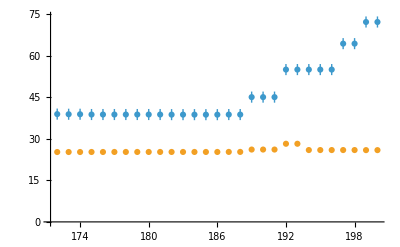

```mathematica
ListPlot[{Transpose@{oneTable[[All,1]],oneTable[[All,-1]]},Transpose@{oneTable[[All,1]],oneTable[[All,-2]]}}]
```

```mathematica
tab[All,"time"][[-5;;-2]]//InputForm
%/. (Head->List)
```

TabularColumn[…]

TabularColumn[<|"Data" -> {4, {{{1252.5, 1258.5, 1264.5, 1270.5}, {}, None}}, None}, 
  "ElementType" -> TypeSpecifier["Quantity"]["Real64", "Seconds"]|>]

```mathematica
tab[[All,"time"]] [[-1]]
```

1276.5 s

```mathematica
tab=ToTabular[d[[16;;-1]],"Rows",<|"ColumnKeys"->d[[15]] /. "[d&t31.12.2035 11:50:55]" -> "time"|>];
tab=CastColumns[%,#->"Quantity"::["Real64","Micrometers"]&/@(sizeRange=d[[15,2;;-1]])];
tab=TransformColumns[tab,{"time"->Function[Round[#time-Max[tab[[All,"time"]]]+UnitConvert["AS_01_end"/. protocol,"Seconds"],.5]]}]
```

```mathematica
Table[Missing[],Length@sizeRange]
```

{Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]}

```mathematica
temp=tab[[207;;-1]]
```

```mathematica
Dimensions@temp
```

{7,32}

```mathematica
TabularRow[Table[Missing[],Dimensions[temp][[2]]]]
```

TabularRow[…]

```mathematica
Insert[temp,TabularRow[Table[Missing[],Dimensions[temp][[2]]]],3]
```

Insert::ins: Cannot insert at position {3} in Tabular[<7,32>]

Insert[,TabularRow[…],3]

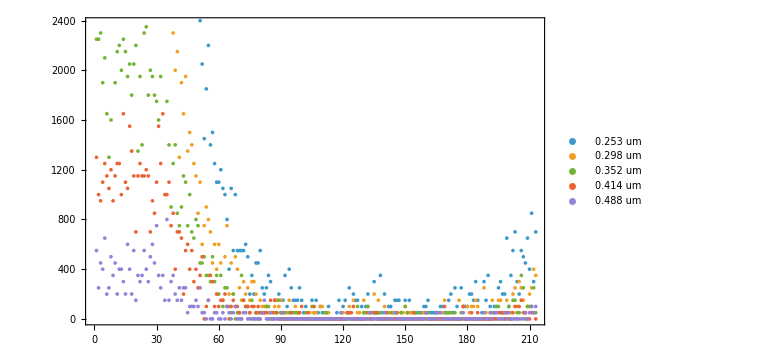

```mathematica
ListPlot[Transpose[Values/@(ConstructColumns[tab,sizeRange[[1;;5]]]//Normal)],myPlotSequence[],PlotLegends->sizeRange[[1;;5]]]
```